Here, we simulate calculate the critical buckling time for an extensible morphoelastic rod that is tethered to a remodelling foundation and subjected to Wnt-based growth.

## ODEs

```mathematica
HorizontalOde[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]*(1+nx[S]),
nx'[S]==k*(1+nx[S])* γ[S]*(x[S]-px[S]),
x[0]==0,nx[0]==R[[1]]},
{x[S],nx[S]},{S,0,L/2},MaxStepSize-> 0.0005][[1]];
{x[S]-L/2}/.Sol/.S->L/2
];

EquilHorizontalSol[R_]:=NDSolve[
{x'[S]==γ[S]*(1+nx[S]),
nx'[S]==k γ[S]*(1+nx[S])*(x[S]-px[S]),
x[0]==0,nx[0]==R[[1]]},
{x,nx},{S,0,L/2}][[1]];
```

## Calculate buckling load

```mathematica
(* Get the data for the initial solution *)
initSolData = Import["~/Documents/MorphoCrypt/Data/planarmorphorodsinextkf0p01L1sol_1"];
y0=initSolData[[300]][[4]];
nx0=initSolData[[300]][[5]];
m0=initSolData[[300]][[8]];
R0 = {nx0, y0, m0};
```

```mathematica
W=Function[s,Exp[-s^2/.16]];
```

```mathematica
Clear[γ,R,SolLagrangian,solLagrangian,EB,px,py];

(* parameters *)
w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
(*Q = 0.1;
n = 2;*)

k=(12*kf*L0^4)/(w*h^3);
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt*W[S];
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
```

```mathematica
Clear[γOld,γNew];
γOld = γ;
sOld[S_]:=S;
```

```mathematica
xComponentsSol
```

{s→InterpolatingFunction[{{0., 0.154382}}, <>],x→InterpolatingFunction[{{0., 0.154382}}, <>],nx→InterpolatingFunction[{{0., 0.154382}}, <>]}

```mathematica
(-dt*W[S])/(1+dt*W[S])/.S-> 0
```

-0.047619

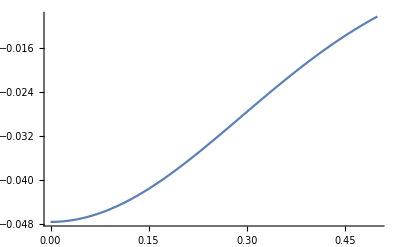

```mathematica
Plot[(-dt*W[S])/(1+dt*W[S]),{S, 0, 0.5}]
```

```mathematica
xComponentsSol = NDSolve[
{x'[S]==(1+dt*W[S])*(1+nx[S]),
s'[S]==(1+dt*W[S])*(1+nx[S]),
nx'[S]==k*(1+dt*W[S])*(1+nx[S])*(x[S]-px[S]),
x[0]==0,s[0]==0,nx[0]==-0.047619047619047616},
{s,x,nx},{S,0,1/2}][[1]];
```

```mathematica
x[0.5]/.xComponentsSol
```

0.254393

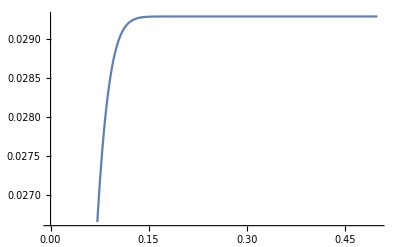

```mathematica
Plot[s[S]/.xComponentsSol ,{S, 0, 0.5}]
```

```mathematica
R0={-dt*W[0]/(1+dt*W[0])};
```

```mathematica
sol=EquilHorizontalSol[R/.Sol];
```

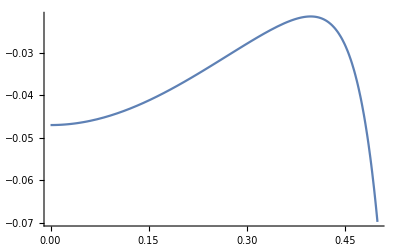

```mathematica
Plot[nx[S]/.sol,{S,0 , 0.5}]
```